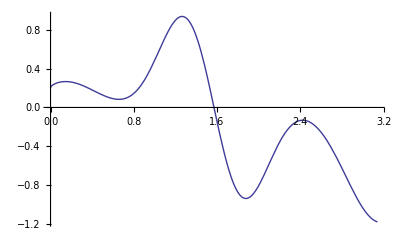

```mathematica
Needs["PlotLegends`"];
f[x_]:=5Cos[x]Sin[x]^10+1/5Cos[x]^9 Exp[Sqrt[x]];
Plot[f[x],{x,0,Pi}]
```

```mathematica
LeftRiemannBoxes[f_,n_,a_,b_]:=
Module[{δ=(b-a)/n},
Table[Polygon[{{a+i δ,0},{a+i δ,f[a+i δ]},{a+(i+1) δ,f[a+i δ]},{a+(i+1)δ,0}}],
{i,0,n-1}]
];
LeftRiemannSum[f_,n_,a_,b_]:=
Module[{δ=(b-a)/n},
N[δ Sum[f[a + i δ],{i,0,n-1}]]
];
```

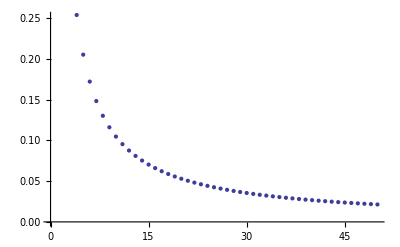

```mathematica
PlotConvergences[f_, xMin_,xMax_,n_, integralFunList_]:=
Module[{trueIntegral,points},
trueIntegral=NIntegrate[f[x],{x,xMin,xMax}];
points=Table[integralFun[f,i,xMin,xMax]-trueIntegral,{integralFun,integralFunList},{i,2,n,2}];
ListPlot[points]
];
PlotConvergences[f,0,Pi,100,{LeftRiemannSum}]
```

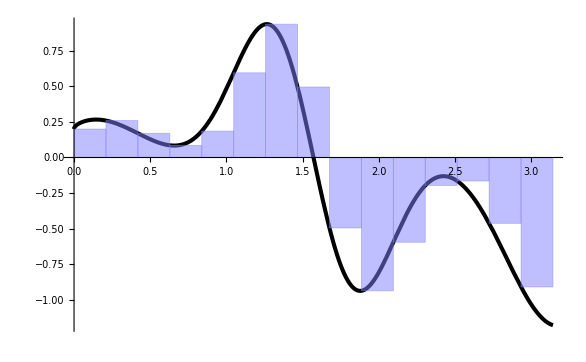

```mathematica
plotIntegralExample[f_,xMin_,xMax_,n_,boxesFun_]:=Show[Plot[f[x],{x,xMin,xMax}, PlotStyle->{Thickness[0.005], Black}],Table[Graphics[{RGBColor[0.5,0.5,1],EdgeForm[Thickness[0.001]], Opacity[0.5],box}],{box,boxesFun[f, n, xMin,xMax]}]]
plotIntegralExample[f, 0,Pi,15,LeftRiemannBoxes]
```

```mathematica
exportIntegralGif[filename_,f_,xMin_,xMax_,n_,boxesFun_]:=
Module[{frames},
frames=Table[plotIntegralExample[f, xMin,xMax,i,boxesFun],{i,1,n}];
Export[filename,frames];
];
```

```mathematica
(*exportIntegralGif["left-riemann-sum.gif",f,0,Pi,100,LeftRiemannBoxes];*)
```

```mathematica
TrapezoidBoxes[f_, n_,a_,b_]:=
Module[{δ=(b-a)/n},
Table[Polygon[{{a+i δ,0},{a+i δ,f[a+i δ]},{a+(i+1) δ,f[a+(i+1) δ]},{a+(i+1)δ,0}}],
{i,0,n-1}]
];
TrapezoidSum[f_,n_,a_,b_]:=
Module[{δ=(b-a)/n},
N[δ Sum[1/2(f[a + i*δ]+f[a + (i+1)*δ]),{i,0,n-1}]]
];
```

```mathematica
Timing[TrapezoidSum[f,100,0,Pi]]
TrapezoidSum[f,100,0,Pi]-NIntegrate[f[x],{x,0,Pi}]
```

{0.132008,-0.313224}

-0.000267256

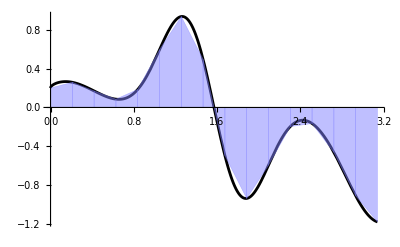

```mathematica
plotIntegralExample[f, 0,Pi,15,TrapezoidBoxes]
```

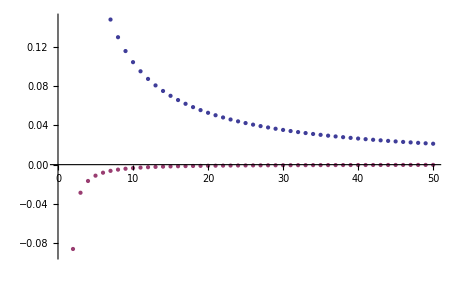

```mathematica
PlotConvergences[f,0,Pi,100,{LeftRiemannSum,TrapezoidSum}]
```

```mathematica
(*exportIntegralGif["trapezoid-sum.gif",f,0,Pi,100,TrapezoidBoxes];*)
```

```mathematica
SimpsonsBoxes[f_, n_,a_,b_]:=
Module[{δ=(b-a)/n,pts,pieces},
pts=Table[{{a+i δ,f[a+i δ]},
{a+(i +1)δ,f[a+(i+1)δ]},
{a+(i+2)δ,f[a+(i+2)δ]}},{i,0,n-1,2}];
pieces=Table[{InterpolatingPolynomial[p,x],p⟦1,1⟧≤ x≤ p⟦3,1⟧},{p,pts}];
Plot[Piecewise[pieces],{x,a,b},Filling->Axis]
];
SimpsonsSum[f_,n_,a_,b_]:=
Module[{δ=(b-a)/n, coefficient},
coefficient[i_?EvenQ]=2;
coefficient[i_?OddQ]=4;
N[(δ/3) (f[a]+f[b]+Sum[(coefficient[i]*f[a + i*δ]),{i,1,n-1}])]
];
```

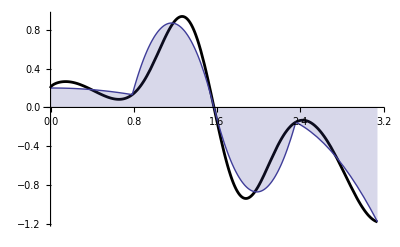

```mathematica
plotIntegralExample2[f_,xMin_,xMax_,n_,boxesFun_]:=Show[Plot[f[x],{x,0,Pi}, PlotStyle->{Thickness[0.005], Black}],Show[boxesFun[f, n, 0,Pi]]];
plotIntegralExample2[f,0,Pi,8,SimpsonsBoxes]
```

```mathematica
exportIntegralGif2[filename_,f_,xMin_,xMax_,n_,boxesFun_]:=
Module[{frames},
frames=Table[plotIntegralExample2[f, xMin,xMax,i,boxesFun],{i,2,n,2}];
Export[filename,frames,"DisplayDurations"->.5];
];
```

```mathematica
(*exportIntegralGif2["simpsons-rule.gif",f,0,Pi,25,SimpsonsBoxes]*)
```

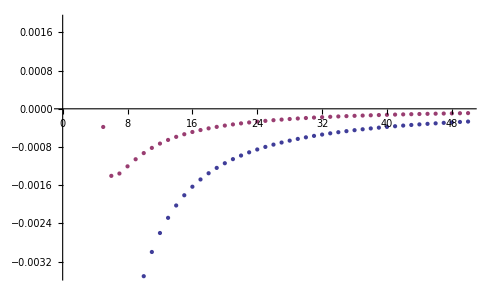

```mathematica
PlotConvergences[f,0,Pi,100,{TrapezoidSum,SimpsonsSum}]
```

```mathematica
compareTiming[f_,n_,a_,b_,integrationFuns_List]:=
Module[{},
ListLinePlot[Table[{i,Timing[integrationFun[f,i,a,b]]⟦1⟧},{integrationFun, integrationFuns},{i,2,n,10}],InterpolationOrder->2, AxesLabel->{"n", "Seconds"}, PlotLegend->integrationFuns,LegendPosition->{1.1,-0.4}]
];
```

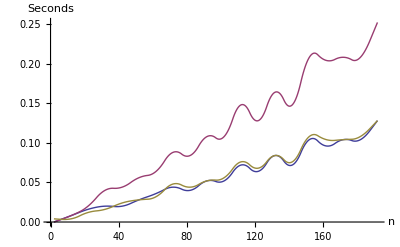

```mathematica
compareTiming[f,200,0,Pi,{LeftRiemannSum,TrapezoidSum,SimpsonsSum}]
```

```mathematica
x=Timing[LeftRiemannSum[f,10000,0,Pi]]
```

{6.70842,-0.31274}

```mathematica
x⟦2⟧-NIntegrate[f[x],{x,0,Pi}]
```

0.000216072

```mathematica
Clear[p];
pts={{1,2},{3,4},{7,-3}};
p[x_]:=(x-1)(x-3)*(-3)/((7-1)(7-3))+(x-7)(x-3)*(2)/((1-7)(1-3))+(x-1)(x-7)*(4)/((3-1)(3-7))
```

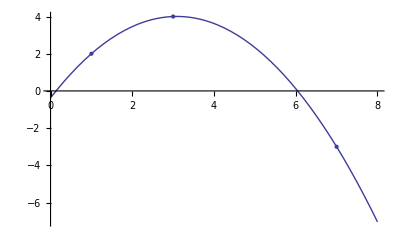

```mathematica
Show[Plot[p[x],{x,0,8}],ListPlot[pts]]
```